```mathematica
AlphaMin=0.10;
AlphaMax=0.29;
AlphaInterval=0.01;
gfacMin=1.;
gfacMax=1.;
gfacInterval=1.;
nbasMin=9;
nbasMax=15;
nbasInterval=6;
nocc=1;
c0=1.0;
c1=0.5;
Table[
Table[
Table[
res[gfac][nbas][omega][alpha][c0][c1]= ReadList["/home/grining/drake-mpfun/python/results/nocc="<>ToString[nocc]<>"nbas="<>ToString[nbas]<>"omega="<>ToString[omega]<>"gfac="<>ToString[NumberForm[gfac, {2,2}]]<>"alpha="<>ToString[NumberForm[alpha, {2,2}]]<>"c0="<>ToString[NumberForm[c0, {2,2}]]<>"c1="<>ToString[NumberForm[c1, {2,2}]]<>".out_FCCD"][[1]]
,{gfac, gfacMin, gfacMax,gfacInterval}];
,{nbas, nbasMin,nbasMax,nbasInterval}];
,{omega,{9}},
{alpha,AlphaMin,AlphaMax,AlphaInterval}];
```

```mathematica
Table[
Res[nbas]=Table[{alpha, res[1.][nbas][9][alpha][1.00][0.50]}, {alpha,AlphaMin,AlphaMax,AlphaInterval}],
{nbas, nbasMin,nbasMax,nbasInterval}];
```

```mathematica
Res[9][[1,2]]-Res[15][[1,2]]
```

2.76276585162954651584785468097786×10^-7

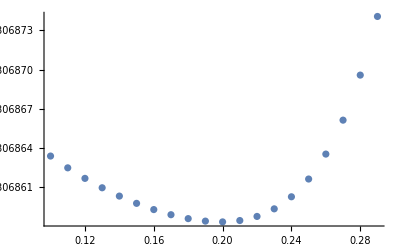
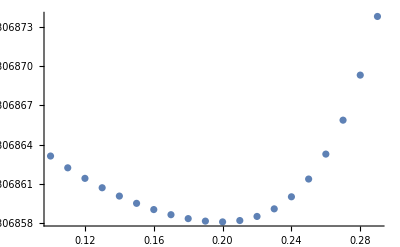

```mathematica
Table[ListPlot[Res[nbas],ImageSize->400], {nbas, nbasMin,nbasMax,nbasInterval}]
```